## Build Transition Network

### CA30 Network

```mathematica
size=3;
CAT=Association[Table[#->CellularAutomaton[30,#,{{{1}}}]&[IntegerDigits[i,2,size]],{i,0,2^size-1}]]
```

<|{0,0,0}→{0,0,0},{0,0,1}→{1,1,1},{0,1,0}→{1,1,1},{0,1,1}→{0,1,0},{1,0,0}→{1,1,1},{1,0,1}→{0,0,1},{1,1,0}→{1,0,0},{1,1,1}→{0,0,0}|>

### Other Networks

```mathematica
CAT=Association[{1->2,2->3,3->5,4->5,5->3,6->5}]
```

<|1→2,2→3,3→5,4→5,5→3,6→5|>

```mathematica
CAT=Association[EdgeRules[g]]
```

<|2→5,3→6,4→2,5→6|>

## Plot Graph

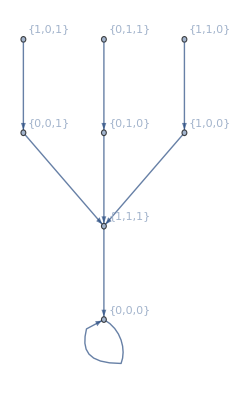

```mathematica
g=Graph[Normal@CAT,VertexLabels->"Name"]
```

## Main Function: Finding ϕ for T

```mathematica
AssociationSort[]
```

```mathematica
ForwardEvolution[$ϕ_,$Vp_,{$vi_,$vj_},$T_]:=Module[{ϕ=$ϕ,Vp=$Vp,vi=$vi,vj=$vj,T=$T},
While[¬KeyExistsQ[ϕ,T[vi]],
ϕ[T[vi]]=T[ϕ[vi]];
vi=T[vi];
vj=T[vj];
Vp=Complement[Vp,{vi}];
];
{ϕ,Vp,vi,vj,T}
]
```

```mathematica
Function
```

```mathematica
observed=<||>
results=<||>
```

<||>

<||>

```mathematica
Findϕ[ϕin_,Vout_,Vin_,T_,d_]:=Module[{ϕ=ϕin,$Vout=Vout,$Vin=Vin,vi,vj,visited=<||>},
If[Vout=={},results[KeySort[ϕ]]=True;Return[],

Do[vi=Vout⟦i⟧;vj=Vin⟦j⟧;
$Vout=Vout;ϕ=ϕin;$Vin=Vin;visited=<||>;(*Initialize*)
ϕ[vi]=vj;

$Vout=Complement[$Vout,{vi}];
$Vin=Complement[$Vin,{vj}];
visited[vj]=True;

If[¬KeyExistsQ[observed,KeySort[ϕ]],

(*{ϕ,Vp,vi,vj,T}=ForwardEvolution[ϕ,Vp,{vi,vj},T];*)

(*Forward Evolution*)
While[¬KeyExistsQ[ϕ,T[vi]]∧¬visited[T[vj]],
ϕ[T[vi]]=T[ϕ[vi]];
vi=T[vi];
vj=T[vj];
$Vout=Complement[$Vout,{vi}];
$Vin=Complement[$Vin,{vj}];
visited[vj]=True;
];

If[¬KeyExistsQ[observed,KeySort[ϕ]],observed[KeySort[ϕ]]=True];

(*If there is no contradiction, then go further search*)
If[ϕ[T[vi]]==T[ϕ[vi]],
$Vout=Complement[$Vout,{T[vi]}];
$Vin=Complement[$Vin,{ϕ[T[vi]]}];
Findϕ[ϕ,$Vout,$Vin,T,d+1]];
]
,{i,1,Length[Vout]},{j,1,Length[Vin]}];
]
]
```

## Experiments

```mathematica
observed=<||>;
results=<||>;
Findϕ[<||>,Keys[CAT],Keys[CAT],CAT,1];
observed=<||>;
Length[Keys[results]]
```

6

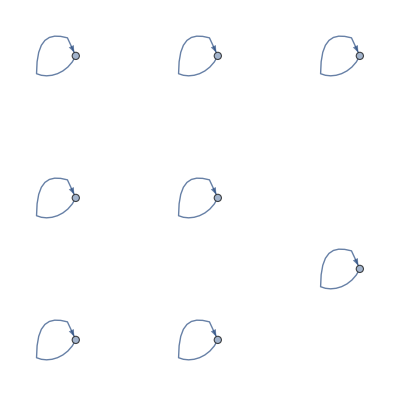
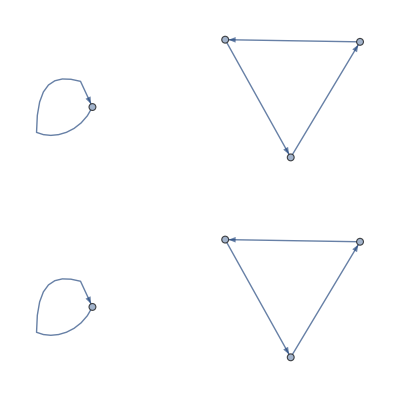
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Graph[Normal[#]]&/@Keys[results]
```

```mathematica
groups=Tally[Sort[Sort/@WeaklyConnectedComponents[#]]&/@(Graph[Normal@#]&/@(Tally[Keys[results]]ᵀ⟦1⟧))];
syms=DeleteDuplicates[Graph[Normal@#]&/@(Keys[results]),IsomorphicGraphQ[#1,#2]&];
syms2=DeleteDuplicates[syms,Sort[Sort/@WeaklyConnectedComponents[#1]]==Sort[Sort/@WeaklyConnectedComponents[#2]]&];
Echo[{Length[syms],Length[syms2],Length[groups]},"Length of {syms,syms2,groups}:"];
```

Length of {syms,syms2,groups}: {3,3,5}

```mathematica
syms2⟦1;;Min[5,Length[syms2]]⟧
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
syms⟦1;;Min[5,Length[syms]]⟧
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
LabelName=Table[IntegerDigits[i,2,3]->i,{i,0,7}];
```

```mathematica
LabelName=Thread[{1,2,3,4,5,6}->{1,2,3,4,5,6}]
```

{1→1,2→2,3→3,4→4,5→5,6→6}

```mathematica
CommunityGraphPlot[g,WeaklyConnectedComponents[syms2⟦2⟧],Method->"Hierarchical",VertexLabels->LabelName]
```

-Graphics-

```mathematica
Multicolumn[CommunityGraphPlot[g,WeaklyConnectedComponents[#],Method->"Hierarchical",VertexLabels->LabelName]&/@syms2,3]
```

-Graphics-

```mathematica
CombineGraphs[g1_,g2_]:=HighlightGraph[Graph[Join[EdgeRules[g1],EdgeRules[g2]],VertexCoordinates->(PropertyValue[{g1,#},VertexCoordinates]&/@VertexList[g1])],EdgeRules[g2],GraphHighlightStyle->"Dashed"]

CombineGraphs[g1_,g2_,"Adaptive"]:=HighlightGraph[Graph[Join[EdgeRules[g1],EdgeRules[g2]]],EdgeRules[g2],GraphHighlightStyle->"Dashed"]
```

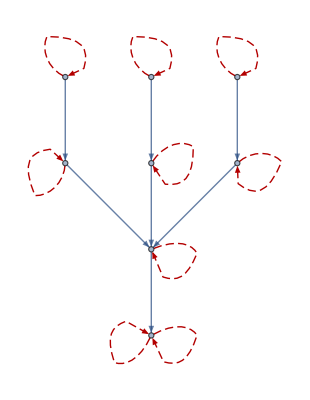
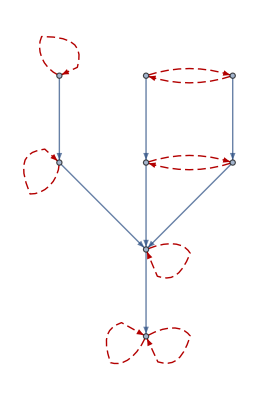
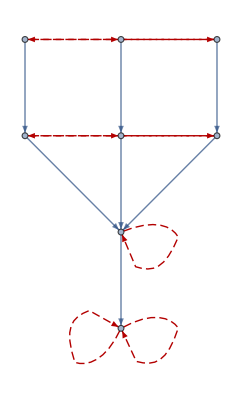
-Graphics- | -Graphics- | -Graphics- |  |

```mathematica
ϕplots=Multicolumn[CombineGraphs[g,#]&/@syms⟦1;;Min[20,Length[syms]]⟧,5]
```

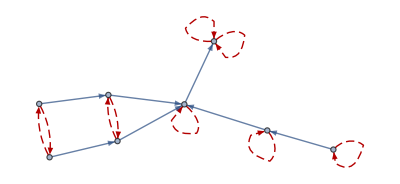
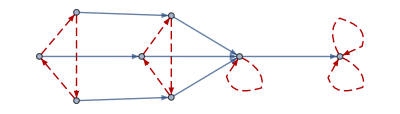
-Graphics- | -Graphics- | -Graphics- |  |

```mathematica
ϕplots=Multicolumn[CombineGraphs[g,#,"Adaptive"]&/@syms⟦1;;Min[20,Length[syms]]⟧,5]
```

## Plots

```mathematica
Length[symclasses]
```

14

```mathematica
symclasses=Gather[syms,Sort[Sort/@WeaklyConnectedComponents[#1]]==Sort[Sort/@WeaklyConnectedComponents[#2]]&];
```

```mathematica
symclassPlot1=Module[{tb=CombineGraphs[g,#]&/@Take[#,Min[Length[#],4]]&/@symclasses},
(*tb⟦1⟧=tb⟦1,1;;4⟧;
tb⟦1,4⟧="...";*)
TableForm[tb,TableHeadings->{CommunityGraphPlot[g,WeaklyConnectedComponents[#⟦1⟧],Method->"Hierarchical"]&/@symclasses,None},TableAlignments->Center]
]
```

-Graphics-

```mathematica
symclassPlot2=Module[{tb=CombineGraphs[g,#,"Adaptive"]&/@Take[#,Min[Length[#],4]]&/@symclasses},
(*tb⟦1⟧=tb⟦1,1;;4⟧;
tb⟦1,4⟧="...";*)
TableForm[tb,TableHeadings->{CommunityGraphPlot[g,WeaklyConnectedComponents[#⟦1⟧],Method->"Hierarchical"]&/@symclasses,None},TableAlignments->Center]
]
```

-Graphics-

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"figures","CoarseGrainPlot1.pdf"}],symclassPlot1]
```

/Users/yanbozhang/项目 & 存档/01 科研项目/CausualEmergence/figures/CoarseGrainPlot1.pdf

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"figures","CoarseGrainPlot2.pdf"}],symclassPlot2]
```

/Users/yanbozhang/项目 & 存档/01 科研项目/CausualEmergence/figures/CoarseGrainPlot2.pdf

## Every Component is loop:

```mathematica
symclasses=Gather[syms,Sort[Sort/@WeaklyConnectedComponents[#1]]==Sort[Sort/@WeaklyConnectedComponents[#2]]&];
```

Test if graph is made by Hamiltonian Graphs:

```mathematica
CyclingGraphQ[graph_]:=AllTrue[HamiltonianGraphQ/@(Subgraph[graph,#]&/@WeaklyConnectedComponents[graph]),#&]
```

```mathematica
Select[syms,CyclingGraphQ[#]&]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
symsH=Select[syms,CyclingGraphQ[#]&];
symclasses2=Gather[symsH,Sort[Sort/@WeaklyConnectedComponents[#1]]==Sort[Sort/@WeaklyConnectedComponents[#2]]&];
```

```mathematica
symclassHPlot1=Module[{tb=CombineGraphs[g,#]&/@Take[#,Min[Length[#],4]]&/@symclasses2},
TableForm[tb,TableHeadings->{CommunityGraphPlot[g,WeaklyConnectedComponents[#⟦1⟧],Method->"Hierarchical"]&/@symclasses2,None},TableAlignments->Center]
]
```

-Graphics-

```mathematica
symclassHPlot2=Module[{tb=CombineGraphs[g,#,"Adaptive"]&/@Take[#,Min[Length[#],4]]&/@symclasses2},
TableForm[tb,TableHeadings->{CommunityGraphPlot[g,WeaklyConnectedComponents[#⟦1⟧],Method->"Hierarchical"]&/@symclasses2,None},TableAlignments->Center]
]
```

-Graphics-

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"figures","CoarseGrainHPlot1.pdf"}],symclassHPlot1]
```

/Users/yanbozhang/项目 & 存档/01 科研项目/CausualEmergence/figures/CoarseGrainHPlot1.pdf

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"figures","CoarseGrainHPlot2.pdf"}],symclassHPlot2]
```

/Users/yanbozhang/项目 & 存档/01 科研项目/CausualEmergence/figures/CoarseGrainHPlot2.pdf